Лабораторная работа №6

Вариант №16. Толстихин Илья, 0В91
Граф  G задан списками  ориетированных (Ded) и неориентированных ребер (Ued), с указанием веса (длины) ребра. Требуется, в соответствии с вариантом задания:
1.  Построить граф;
2.  Найти кратчайший путь от вершины v1 до вершины v2 и его длину ;
3.  Найти кратчайший замкнутый маршрут (маршрут коммивояжера) от вершины v1 через вершины v2,v3,v4 (в любой последовательности) и его длину  ;
4.  Отобразить найденные маршруты на графе.

Вариант 16
Ded={{41,33,6},{60,52,4},{39,31,3},{47,39,5},{63,55,1},{59,58,1},{61,60,1},{2,10,5},{26,34,4},{22,23,6},{43,51,3},{44,52,4},{29,37,3},{23,31,3},{47,55,1},{57,58,2}}
Ued={{1,2,3},{1,9,4},{2,3,5},{9,17,1},{17,25,6},{4,5,3},{25,33,2},{5,6,4},{6,7,4},{41,49,4},{49,57,3},{9,10,3},{10,11,1},{10,18,5},{18,26,6},{12,13,3},{13,14,1},{34,42,4},{42,50,2},{15,16,1},{17,18,5},{3,11,2},{18,19,1},{11,19,5},{19,20,6},{20,21,4},{27,35,2},{21,22,4},{35,43,5},{23,24,5},{51,59,5},{25,26,3},{4,12,6},{26,27,3},{27,28,2},{20,28,1},{29,30,6},{36,44,4},{30,31,3},{33,34,1},{5,13,2},{34,35,4},{35,36,6},{21,29,6},{37,45,4},{38,39,4},{45,53,2},{39,40,5},{41,42,3},{42,43,3},{14,22,4},{22,30,6},{44,45,4},{30,38,5},{45,46,3},{38,46,2},{46,47,6},{46,54,6},{47,48,3},{54,62,6},{49,50,6},{7,15,5},{50,51,4},{51,52,2},{52,53,5},{53,54,2},{54,55,2},{55,56,2},{8,16,6},{16,24,5},{24,32,4},{32,40,6},{61,62,5},{40,48,1},{48,56,6},{63,64,1},{56,64,4}}
{v1,v2,v3,v4}={4,57,2,39}

Задание 1.  Построить граф

```mathematica
v1=4;v2=57;v3=2;v4=39;
```

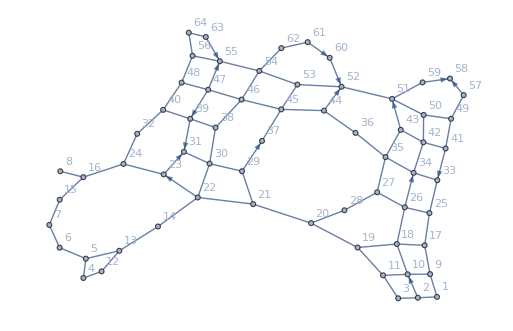

```mathematica
G=Graph[{ 41->33,60->52,39->31,47->39,63->55,59->58,61->60,2->10,26->34,22->23,43->51,44->52,29->37,23->31,47->55,57->58,1<->2,1<->9,2<->3,9<->17,17<->25,4<->5,25<->33,5<->6,6<->7,41<->49,49<->57,9<->10,10<->11,10<->18,18<->26,12<->13,13<->14,34<->42,42<->50,15<->16,17<->18,3<->11,18<->19,11<->19,19<->20,20<->21,27<->35,21<->22,35<->43,23<->24,51<->59,25<->26,4<->12,26<->27,27<->28,20<->28,29<->30,36<->44,30<->31,33<->34,5<->13,34<->35,35<->36,21<->29,37<->45,38<->39,45<->53,39<->40,41<->42,42<->43,14<->22,22<->30,44<->45,30<->38,45<->46,38<->46,46<->47,46<->54,47<->48,54<->62,49<->50,7<->15,50<->51,51<->52,52<->53,53<->54,54<->55,55<->56,8<->16,16<->24,24<->32,32<->40,61<->62,40<->48,48<->56,63<->64,56<->64}, EdgeWeight->{41->33->6,60->52->4,39->31->3,47->39->5,63->55->1,59->58->1,61->60->1,2->10->5,26->34->4,22->23->6,43->51->3,44->52->4,29->37->3,23->31->3,47->55->1,57->58->2,1<->2->3,1<->9->4,2<->3->5,9<->17->1,17<->25->6,4<->5->3,25<->33->2,5<->6->4,6<->7->4,41<->49->4,49<->57->3,9<->10->3,10<->11->1,10<->18->5,18<->26->6,12<->13->3,13<->14->1,34<->42->4,42<->50->2,15<->16->1,17<->18->5,3<->11->2,18<->19->1,11<->19->5,19<->20->6,20<->21->4,27<->35->2,21<->22->4,35<->43->5,23<->24->5,51<->59->5,25<->26->3,4<->12->6,26<->27->3,27<->28->2,20<->28->1,29<->30->6,36<->44->4,30<->31->3,33<->34->1,5<->13->2,34<->35->4,35<->36->6,21<->29->6,37<->45->4,38<->39->4,45<->53->2,39<->40->5,41<->42->3,42<->43->3,14<->22->4,22<->30->6,44<->45->4,30<->38->5,45<->46->3,38<->46->2,46<->47->6,46<->54->6,47<->48->3,54<->62->6,49<->50->6,7<->15->5,50<->51->4,51<->52->2,52<->53->5,53<->54->2,54<->55->2,55<->56->2,8<->16->6,16<->24->5,24<->32->4,32<->40->6,61<->62->5,40<->48->1,48<->56->6,63<->64->1,56<->64->4}, VertexLabels->"Name"]
```

Задание 2.   Найти кратчайший путь от вершины v1 до вершины v2 и его длину

```mathematica
SW=FindShortestPath[G,v1,v2]
GraphDistance[G,v1,v2]
```

{4,5,13,14,22,21,20,28,27,35,34,42,41,49,57}

41.

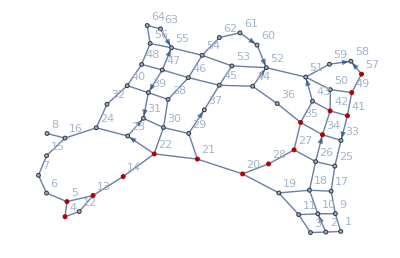

```mathematica
HighlightGraph[G,SW]
```

Задание 3.

```mathematica
v:={};t:={};
P=Permutations[{v2,v3,v4}]
```

{{57,2,39},{57,39,2},{2,57,39},{2,39,57},{39,57,2},{39,2,57}}

```mathematica
For[i=1,i≤Length[P], i++, {nm:=GraphDistance[G,v1,Part[Part[P,i],1]]+GraphDistance[G,Part[Part[P,i],1],Part[Part[P,i],2]]+GraphDistance[G,Part[Part[P,i],2],Part[Part[P,i],3]]+GraphDistance[G,Part[Part[P,i],1],v1], If[nm<Infinity,{t=nm,v=P[[i]]}]}]
Way=Join[{v1},v,{v1}]
```

{4,39,2,57,4}

```mathematica
tour:={};L:={}
For[i=1,i< Length[Way],i++,
{L=FindShortestPath[G,Way[[i]],Way[[i+1]]],If[i==1,tour=Join[tour,L],tour=Join[tour,Drop[L,1]]]}]
```

```mathematica
tour
t
```

{4,5,13,14,22,30,38,39,31,30,22,21,20,19,11,3,2,1,9,17,25,33,34,42,41,49,57,49,41,42,43,35,27,28,20,21,22,14,13,5,4}

116.

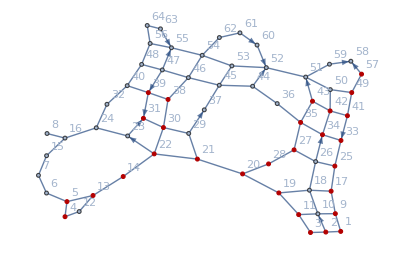

```mathematica
HighlightGraph[G,tour]
```